```mathematica
(*  
Implementation of the Chain complexes from paper by Vidick et al 2022. 

The chain comlexses are defined via the quadpartite left-right Cayley complex, which can be randomly generated by providing random generators with a fix group. I.e. Random Cayley graphs are expanders from Aldous conjectures... 

Can also be used to incorprate the PK codes with providing explicit cobnstruction of the PSL & PGL group operation. 

Need: find some Tanner codes. Currently default to be random codes. 
*)
```

```mathematica
(*

Base Cayley graphs, currently assumed to be randomly generated from Dn with fixed degree 3

*)

Basegenertors = RandomPermutation[4, 2]



(*Basegenertors = {Cycles[{{1,2}}], Cycles[{{2,3}}]}*)
BaseGroup =  PermutationGroup[Basegenertors]
BaseGroup // GroupOrder

(*BaseCayley = CayleyGraph[BaseGroup] *)
```

{Cycles[{{2,3,4}}],Cycles[{{1,3,2}}]}

PermutationGroup[{Cycles[{{2,3,4}}],Cycles[{{1,3,2}}]}]

12

```mathematica
(*BaseAdj = AdjacencyMatrix[BaseCayley]  // MatrixForm; *)
Basedegree = Length @ Basegenertors;
Basedim =  BaseGroup // GroupOrder; 
(*Basedim =  VertexCount[BaseCayley];*)
Basevertices  = BaseGroup// GroupElements;
```

```mathematica
(*
Now We build the Tanner graph of  and 
*)
BaseEgdeLeft[idx_] := Module[{ lst , g, i, j ,h, generator}, 
lst = {};
g = Basevertices[[idx]]; 	
				
For [j =1, j <= Length @ Basevertices , j++, 
		h = Basevertices[[j]];
	 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];

If[h== PermutationProduct[generator,g], AppendTo[lst, {idx, j, i}]]
] ;
];
lst
]; 


BaseEgdeRight[idx_] := Module[{ lst , g, i, j ,h, generator}, 
lst = {};
g = Basevertices[[idx]]; 	
				
For [j =1, j <= Length @ Basevertices , j++, 
		h = Basevertices[[j]];
	 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];

If[h== PermutationProduct[g, generator], AppendTo[lst, {idx, j, i}]]
] ;
];
lst
]; 

EdgesLeft = Flatten[Table[BaseEgdeLeft[i], {i, 1, Basedim}], 1] (* src, dest, path *)
EdgesRight = Flatten[Table[BaseEgdeRight[i], {i, 1, Basedim}], 1]
```

{{1,2,1},{1,7,2},{2,3,1},{2,10,2},{3,1,1},{3,4,2},{4,6,1},{4,11,2},{5,1,2},{5,4,1},{6,5,1},{6,8,2},{7,5,2},{7,8,1},{8,9,1},{8,12,2},{9,2,2},{9,7,1},{10,9,2},{10,12,1},{11,3,2},{11,10,1},{12,6,2},{12,11,1}}

{{1,2,1},{1,7,2},{2,3,1},{2,8,2},{3,1,1},{3,9,2},{4,2,2},{4,7,1},{5,1,2},{5,9,1},{6,3,2},{6,8,1},{7,5,2},{7,10,1},{8,4,2},{8,12,1},{9,6,2},{9,11,1},{10,4,1},{10,12,2},{11,5,1},{11,10,2},{12,6,1},{12,11,2}}

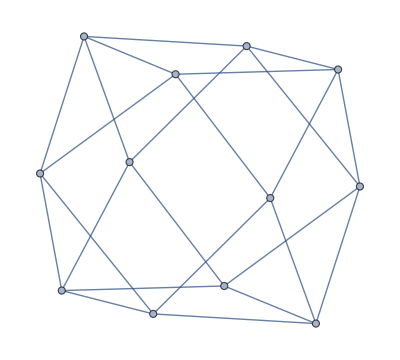

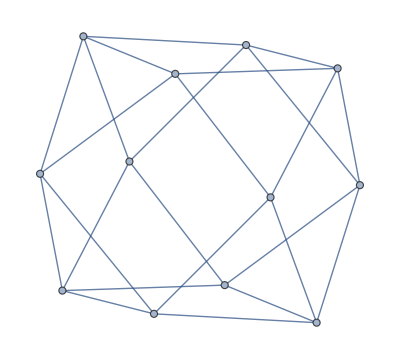

```mathematica
(*
The left and right bartitiple graph: Note that 
*)
LeftGVE = Graph[Table[i, {i, 1, Basedim}], EdgesLeft[[All, {1,2}]] ]
RightGVE = Graph[Table[i, {i, 1, Basedim}], EdgesRight[[All, {1, 2}]]]
LeftGVE = AdjacencyMatrix[LeftGVE];
RightGVE = AdjacencyMatrix[RightGVE];
```

```mathematica
(*
Now We produce the Left and Right GEF 
*)

GetIncEdgesLeft[idx_] :=  Module[{ lst , g1,g2, i, generator,h1dex, h2dex  }, (* use the StoreInfoRight *)
lst = {};
g1 = Basevertices[[idx[[1]]]];
(*Print[g1]*);
g2 = Basevertices[[idx[[2]]]];
				 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];
h1dex = Flatten[Position[Basevertices, PermutationProduct[generator, g1]]][[1]]; 
(*Print[ PermutationProduct[generator, g1]]; *)
h2dex = Flatten[Position[Basevertices, PermutationProduct[generator, g2]]][[1]]; 

If[MemberQ[EdgesRight, {h1dex, h2dex, idx[[3]]}], AppendTo[lst, {idx, {h1dex, h2dex, idx[[3]]}}]]
] ;
lst
]; 

GetIncEdgesRight[idx_] :=  Module[{ lst , g1,g2, i, generator,  h1dex, h2dex}, (* use the StoreInfoRight *)
lst = {};
g1 = Basevertices[[idx[[1]]]];
(*Print[g1]*);
g2 = Basevertices[[idx[[2]]]];
				 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];
h1dex = Flatten[Position[Basevertices, PermutationProduct[ g1, generator]]][[1]]; 
(*Print[ PermutationProduct[generator, g1]]; *)
h2dex = Flatten[Position[Basevertices, PermutationProduct[ g2, generator]]][[1]]; 

If[MemberQ[EdgesLeft, {h1dex, h2dex, idx[[3]]}], AppendTo[lst, {idx, {h1dex, h2dex, idx[[3]]}}]]
] ;
lst
]; 

FacesLeft = Flatten[Table[GetIncEdgesLeft[EdgesRight[[i]]], {i, 1, Length @ EdgesRight}],1]; 
FacesRight = Flatten[Table[GetIncEdgesRight[EdgesLeft[[i]]], {i, 1, Length @ EdgesLeft}],1]; 
(*producing the faces given by f = (g, ag, gb, agb)*)
Faces = Module[ { lst, g, a,b, i, j, k, pos2, pos3, pos4 }, 
lst = {};
For[i=1, i <= Basedim, i++, 
g = Basevertices[[i]];
For[j=1, j <= Basedegree, j++,
a= Basegenertors[[j]];

For[k =1, k <= Basedegree, k++, 
b= Basegenertors[[k]];
pos2 = Flatten[ Position[ Basevertices, PermutationProduct[a, g ]]][[1]];
pos3 =  Flatten[Position[ Basevertices, PermutationProduct[ g, b ]]][[1]];
pos4=  Flatten[Position[ Basevertices, PermutationProduct[a, g, b ]]][[1]];
AppendTo[lst, {i, pos2, pos3, pos4}]
];
];
];
lst
]
Length @ FacesLeft ==Length @ Faces == Length @ FacesRight (* It is important to make sure that the labelings of faces are in the same order *)
```

{{1,2,2,3},{1,2,7,8},{1,7,2,10},{1,7,7,5},{2,3,3,1},{2,3,8,9},{2,10,3,4},{2,10,8,12},{3,1,1,2},{3,1,9,7},{3,4,1,7},{3,4,9,2},{4,6,7,8},{4,6,2,3},{4,11,7,5},{4,11,2,10},{5,4,9,7},{5,4,1,2},{5,1,9,2},{5,1,1,7},{6,5,8,9},{6,5,3,1},{6,8,8,12},{6,8,3,4},{7,8,10,12},{7,8,5,4},{7,5,10,9},{7,5,5,1},{8,9,12,11},{8,9,4,6},{8,12,12,6},{8,12,4,11},{9,7,11,10},{9,7,6,5},{9,2,11,3},{9,2,6,8},{10,12,4,6},{10,12,12,11},{10,9,4,11},{10,9,12,6},{11,10,5,4},{11,10,10,12},{11,3,5,1},{11,3,10,9},{12,11,6,5},{12,11,11,10},{12,6,6,8},{12,6,11,3}}

True

```mathematica
(*
Now Build the Left and Right GEF
*)
```

```mathematica
LeftGEF = Module[{M1, edgeleft, rowidxleft, colidxleft},

M1 = Table[ 0 * i *j , {i, 1, Basedegree * Basedim}, {j, 1,  Basedegree * Basedim}];   
For[i=1, i <= Length @ FacesLeft, i++,
edgeleft = FacesLeft[[i]]; 
(*edgeright = IncEdgesRight[[i]]; *)
rowidxleft = (edgeleft[[1]][[1]] -1) * Basedegree +  edgeleft[[1]][[3]]; 
colidxleft = (edgeleft[[2]][[1]] -1) * Basedegree +  edgeleft[[2]][[3]] ; 
(*rowidxright = edgeright[[1]][[1]] * edgeright[[1]][[3]]; 
colidxright = edgeright[[2]][[1]] * edgeright[[2]][[3]]; *)

M1[[rowidxleft,colidxleft ]] =1 ; 
M1[[colidxleft, rowidxleft ]] =1 ; 
(*M1[[rowidxright,colidxright ]]=1;*)
];
M1
]; 

TannLeftGEF[HA_] :=  Module[{ mat , g1,g2, i, generator,h1dex, h2dex , edge, matrix }, (* use  *)
mat = {}; 
				 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];
matrix = ConstantArray[0, {Length @ EdgesRight, Length @ EdgesRight}]; 
For[j =1, j<= Length @ EdgesRight, j++, 
edge = EdgesRight[[j]]; 
g1 = Basevertices[[edge[[1]]]]; 
g2 = Basevertices[[edge[[2]]]]; 
h1dex = Flatten[Position[Basevertices, PermutationProduct[generator, g1]]][[1]]; 
(*Print[ PermutationProduct[generator, g1]]; *)
h2dex = Flatten[Position[Basevertices, PermutationProduct[generator, g2]]][[1]]; 

If[MemberQ[EdgesRight, {h1dex, h2dex, edge[[3]]}],
matrix[[(edge[[1]]-1)* Length @ Basegenertors + edge[[3]], (h1dex-1)* Length @ Basegenertors + edge[[3]]]] =1
];
] ;
(*Print[matrix // Dimensions];*)
matrix = KroneckerProduct[matrix, HA[[i]]]; 
AppendTo[mat, matrix];
]; 
mat = Catenate[mat]; 
(*Print[mat // Dimensions];*)
mat
];

HA = ArrayReshape[RandomSample[Join[ConstantArray[1,Length @ Basegenertors],ConstantArray[0,4 *Length @ Basegenertors  -Length @ Basegenertors]]], {Length @ Basegenertors, 4}];
HA // Dimensions
TannLeftGEF[HA]  // Dimensions
```

```mathematica
TannRightGEF[HA_] :=  Module[{ mat , g1,g2, i, generator,h1dex, h2dex , edge, matrix }, (* use  *)
mat = {}; 
				 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];
matrix = ConstantArray[0, {Length @ EdgesLeft, Length @ EdgesLeft}]; 
For[j =1, j<= Length @ EdgesLeft, j++, 
edge = EdgesLeft[[j]]; 
g1 = Basevertices[[edge[[1]]]]; 
g2 = Basevertices[[edge[[2]]]]; 
h1dex = Flatten[Position[Basevertices, PermutationProduct[g1, generator]]][[1]]; 
(*Print[ PermutationProduct[generator, g1]]; *)
h2dex = Flatten[Position[Basevertices, PermutationProduct[g2, generator]]][[1]]; 

If[MemberQ[EdgesLeft, {h1dex, h2dex, edge[[3]]}],
matrix[[(edge[[1]]-1)* Length @ Basegenertors + edge[[3]], (h1dex-1)* Length @ Basegenertors + edge[[3]]]] =1
];
] ;
(*Print[matrix // Dimensions];*)
matrix = KroneckerProduct[matrix, HA[[i]]]; 
AppendTo[mat, matrix];
]; 
mat = Catenate[mat]; 
(*Print[mat // Dimensions];*)
mat
];
HB= ArrayReshape[RandomSample[Join[ConstantArray[1,Length @ Basegenertors],ConstantArray[0,6*Length @ Basegenertors  -Length @ Basegenertors]]], {Length @ Basegenertors, 6}];
HB // Dimensions
TannRightGEF[HB]  // Dimensions
```

{2,6}

{48,144}

```mathematica
RightGEF = Module[{M1, edgeright, rowidxright, colidxright},

M1 = Table[ 0 * i *j , {i, 1, Basedegree * Basedim}, {j, 1,  Basedegree * Basedim}];   
For[i=1, i <= Length @ FacesRight, i++,
(*edgeleft = IncEdgesLeft[[i]]; *)
edgeright = FacesRight[[i]]; 
(*rowidxleft = edgeleft[[1]][[1]] * edgeleft[[1]][[3]]; 
colidxleft = edgeleft[[2]][[1]] * edgeleft[[2]][[3]] ; *)
rowidxright = (edgeright[[1]][[1]] - 1) *  Basedegree+  edgeright[[1]][[3]]; 
colidxright = (edgeright[[2]][[1]] -1)* Basedegree +  edgeright[[2]][[3]]; 

(*M1[[rowidxleft,colidxleft ]] =1 ; *)
M1[[rowidxright,colidxright ]]=1;
M1[[colidxright, rowidxright ]]=1;

];
M1 
];
```

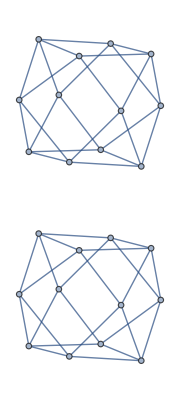

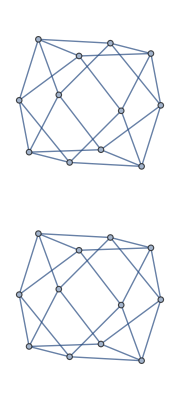

```mathematica
(* These should also be undirected graph *)
AdjacencyGraph[LeftGEF]
AdjacencyGraph[RightGEF]
IsomorphicGraphQ[AdjacencyGraph[LeftGEF], AdjacencyGraph[RightGEF]]  (*In general not the same graph*)
```

```mathematica
(*


Build the Incidence graph 


*)
```

```mathematica
LeftGEFInc = Transpose[IncidenceMatrix[AdjacencyGraph[LeftGEF]]] ;

RightGEFInc = Transpose[IncidenceMatrix[AdjacencyGraph[RightGEF]]] ;
```

```mathematica
(*
These are Special Tanner graphs. Given the (src, dest, path), we are able to prescribe them quantum CSS codes and build the Chain Complexes. 
Recall that the tanner codes are defined by 

*)
```

```mathematica
(*
The chain complex is well difined iff 
In our case, we have that  

i.e defining the quantum tanner graphs with faces -> edges -> vertices

*)

TanLeftGEF[Ca_] := KroneckerProduct[LeftGEFInc, Ca];
TanRightGEF[Cb_] := KroneckerProduct[RightGEF, Cb];

TanLeftGVE[Cb_] := KroneckerProduct[LeftGVE, Cb ];
TanRightGVE[Ca_] := KroneckerProduct[RightGVE , Ca];
```

```mathematica
(*
Testing given random codes 
*)
```

```mathematica
ma=3 ;
mb=5;
Ca=RandomSample[Join[ConstantArray[1,1],ConstantArray[0,ma -1]]];
Cb=RandomSample[Join[ConstantArray[1,2],ConstantArray[0,mb -2]]];
```

```mathematica
TanLeftGEF[Ca] // Dimensions
```

{48,72}